# Donald Ervin Knuth the Art of Computer Programming Volume 4A Combinatorial Optimization Part 1

Peter Burbery

I implement Donald Knuths calculations and my own ideas inspired by the book The Art of Computer Programming Volume 4A Combinatorial Algorithms Part 1 by Donald Ervin Knuth, professor emeritus of computer science at Stanford University.

## Graphs From Words

Lewis Carrol word links or doublets.

change 1 letter at a time.

Find all words that are 5 letters long

```mathematica
wordData=Select[StringLength[#]==5&][WordList[]]
```

{aback,abaft,abase,abash,abate,abbey,abbot,abeam,abhor,abide,abode,abort,about,above,abuse,abuzz,abyss,acorn,acres,acrid,actor,acute,adage,adapt,adder,addle,adept,adieu,adios,adman,admit,admix,adobe,adopt,adore,adorn,adult,aegis,aerie,affix,afire,afoot,afoul,after,again,agape,agate,agave,agent,aggro,agile,aging,aglow,agony,agree,ahead,aided,aired,aisle,alack,alarm,album,alder,alert,algae,algal,alias,alibi,alien,align,alike,alive,alkyd,allay,alley,allot,allow,alloy,aloes,aloft,aloha,alone,along,aloof,aloud,alpha,altar,alter,amass,amaze,amber,ambit,amble,amend,amide,amigo,amine,amino,amiss,amity,among,amour,ample,amply,amuse,anent,angel,anger,angle,angry,angst,anion,anise,ankle,annex,annoy,annul,anode,antic,antsy,anvil,aorta,apace,apart,aphid,apish,apnea,apple,apply,April,apron,aptly,arbor,arced,ardor,areal,arena,argon,argot,argue,arise,armed,armor,aroma,arras,array,arrow,arson,ASCII,ascot,ashen,aside,askew,aspen,aspic,assay,asset,aster,astir,atilt,atlas,atoll,atone,attar,attic,audio,audit,auger,aught,augur,aural,auric,auxin,avail,avast,avert,avian,avoid,await,awake,award,aware,awash,awful,awing,axial,axiom,azure,babel,baccy,bacon,badge,badly,bagel,baggy,bairn,baize,baked,baker,baldy,balky,bally,balmy,balsa,banal,bandy,banjo,banns,bared,barge,barmy,baron,basal,based,basic,BASIC,basil,basin,basis,basso,baste,batch,bated,bathe,batik,baton,batty,baulk,bawdy,bayou,beach,beads,beady,beard,beast,beats,beaut,bebop,bedim,beech,beefy,beery,befit,befog,beget,begin,begum,beige,being,belay,belch,belie,belle,belly,below,bench,bends,beret,berry,berth,beryl,beset,besom,betel,bevel,bezel,bible,biddy,bidet,bight,bigot,bijou,bilge,billy,binge,bingo,biota,biped,birch,birth,bison,biter,bitty,black,blade,blahs,blame,bland,blank,blare,blase,blast,blaze,bleak,blear,bleat,bleed,bleep,blend,bless,blimp,blind,blini,blink,bliss,blitz,bloat,block,bloke,blond,blood,bloom,blown,blowy,blues,bluff,blunt,blurb,blurt,blush,board,boast,bobby,boffo,bogey,boggy,bogus,bolus,bonce,bones,bongo,bonny,bonus,booby,boost,booth,booty,booze,boozy,borax,bored,borer,boron,bosom,boson,bossy,botch,bough,bound,bowed,bowel,bower,bowls,boxed,boxer,brace,bract,braid,brain,brake,brand,brash,brass,brave,bravo,brawl,brawn,braze,bread,break,bream,breed,breve,bribe,brick,bride,brief,brier,brill,brine,bring,brink,briny,brisk,broad,broil,broke,bronc,brood,brook,broom,broth,brown,bruin,bruit,brunt,brush,brute,buddy,budge,buggy,bugle,build,built,bulge,bulgy,bulky,bully,bumpy,bunch,bunny,burgh,burly,burnt,burro,bursa,burst,busby,bushy,busty,butte,butty,buxom,buyer,bylaw,byway,cabal,caber,cabin,cable,cacao,cache,caddy,cadet,cadge,cadre,cagey,cairn,calla,calve,calyx,camel,cameo,campy,canal,candy,canny,canoe,canon,canto,caper,capon,carat,cards,caret,cargo,carob,carol,carom,carry,carve,cased,caste,catch,cater,catty,caulk,cause,cavil,cease,cecal,cecum,cedar,cello,chafe,chaff,chain,chair,chalk,champ,chant,chaos,chard,charm,chart,chary,chase,chasm,cheap,cheat,check,cheek,cheep,cheer,chert,chess,chest,chewy,chick,chide,chief,child,chili,chill,chime,chimp,china,chine,chino,chips,chirp,chive,chock,choir,choke,chomp,chord,chore,chuck,chuff,chump,chunk,churl,churn,chute,chyme,cider,cigar,cinch,circa,cissy,civet,civic,civil,clack,claim,clamp,clams,clang,clank,clash,clasp,class,clean,clear,cleat,cleft,clerk,clews,click,cliff,climb,clime,cling,clink,cloak,clock,clomp,clone,close,cloth,cloud,clout,clove,clown,cluck,clump,clunk,coach,coast,COBOL,cobra,cocci,cocky,cocoa,coder,codex,colic,colon,color,combo,comer,comet,comfy,comic,comma,conch,condo,conga,conic,copra,copse,coral,cords,corer,corgi,corny,corps,costs,couch,cough,count,coupe,court,coven,cover,covet,covey,cower,coyly,coypu,cozen,crabs,crack,craft,cramp,crane,crank,crape,crash,crass,crate,crave,crawl,craze,crazy,creak,cream,credo,creed,creek,creel,creep,crepe,cress,crest,crick,crier,crime,crimp,crisp,croak,crock,croft,crone,crony,crook,croon,cross,croup,crowd,crown,crude,cruel,cruet,crumb,cruse,crush,crust,crypt,cubic,cubit,cumin,cupid,cuppa,cured,curie,curio,curly,curry,curse,curve,curvy,cushy,cycle,cyder,cynic,dacha,daddy,daily,dairy,daisy,dally,dance,dandy,darts,dated,datum,daunt,davit,dazed,deary,death,debar,debit,debug,debut,decaf,decal,decay,decor,decoy,decry,deeds,defer,degas,deify,deign,deism,deist,deity,delay,delft,delta,delve,demob,demon,demur,denim,dense,depot,depth,derby,deter,detox,deuce,devil,dhoti,diary,dicey,digit,dimer,dimly,dinar,diner,dingo,dingy,dinky,diode,dirge,dirty,disco,dishy,ditch,ditto,ditty,divan,diver,divot,divvy,dizzy,dodge,dodgy,doggy,dogie,dogma,doily,doing,dolly,dolor,domed,donor,doped,dopey,dosed,dotty,doubt,dough,douse,dowdy,dowel,dower,downy,dowry,dowse,doyen,dozen,draft,drain,drake,drama,drape,drawl,drawn,dread,dream,drear,dregs,dress,dried,drier,drift,drill,drink,drive,droll,drone,drool,droop,dross,drove,drown,drunk,drupe,dryad,dryer,dryly,ducal,ducat,duchy,ducky,dully,dummy,dumps,dumpy,duple,durum,dusky,dusty,duvet,dwarf,dweeb,dwell,dying,eager,eagle,eared,early,earth,eased,easel,eater,eaves,ebony,eclat,edema,edged,edger,edict,edify,educe,eerie,egret,eider,eight,eject,eland,elate,elbow,elder,elect,elegy,elfin,elide,elite,elope,elude,elver,elves,email,embed,ember,emcee,emend,emery,emote,empty,enact,ended,endow,endue,enema,enemy,enjoy,ennui,ensue,enter,entry,envoy,epoch,epoxy,equal,equip,erase,erect,ergot,erode,error,erupt,essay,ester,ether,ethic,ethos,ethyl,etude,evade,event,every,evict,evoke,exact,exalt,excel,exert,exile,exist,expat,expel,extol,extra,exude,exult,fable,faced,facet,faddy,faded,faint,fairy,faith,faker,fakir,falls,false,famed,fancy,farad,farce,fatal,fated,fatty,fatwa,fault,fauna,favor,fazed,feast,fecal,feces,feign,feint,fella,felon,femur,fence,feral,ferny,ferry,fetal,fetch,fetid,fetus,fever,fewer,fiber,fichu,field,fiend,fiery,fifth,fifty,fight,filch,filer,filly,filmy,filth,final,finch,finer,finis,fired,first,firth,fishy,fitly,fiver,fives,fixed,fixer,fizzy,fjord,flack,flail,flair,flake,flaky,flame,flank,flaps,flare,flash,flask,flats,fleck,fleet,flesh,flick,flier,flies,fling,flint,flirt,float,flock,flood,floor,flora,floss,flour,flout,fluff,fluid,fluke,fluky,flume,flunk,flush,flute,foamy,focal,focus,foggy,foist,folio,folks,folly,foray,force,forge,forgo,forte,forth,forty,forum,found,fount,foyer,frail,frame,franc,frank,fraud,freak,fresh,friar,fried,fries,frill,frisk,frizz,frock,frond,front,frost,froth,frown,fruit,frump,fryer,fudge,fugal,fugue,fully,fumed,fumes,funds,funky,funny,furor,furry,furze,fused,fusee,fussy,fusty,futon,fuzzy,gabby,gable,gaffe,gaily,gamin,gamma,gammy,gamut,gassy,gator,gaudy,gaunt,gauze,gauzy,gavel,gawky,gecko,gelid,genie,genre,genus,geode,getup,ghost,ghoul,giant,giddy,gimpy,girth,given,giver,glace,glade,gland,glans,glare,glass,glaze,gleam,glean,glide,glint,glitz,gloat,globe,gloom,glory,gloss,glove,glued,gluey,gluon,glyph,gnarl,gnash,gnome,godly,gofer,going,golly,goner,goody,gooey,goofy,goose,gorge,gorse,gouge,gourd,gouty,grace,grade,graft,grail,grain,grand,grant,grape,graph,grasp,grass,grate,grave,gravy,graze,great,grebe,greed,green,greet,grief,grill,grime,grimy,grind,gripe,grist,grits,groan,groat,groin,groom,grope,gross,group,grout,grove,growl,grown,gruel,gruff,grump,grunt,guano,guard,guava,guess,guest,guide,guild,guile,guilt,guise,gulag,gulch,gully,gumbo,gummy,gunny,guppy,gushy,gusto,gusty,gutsy,gypsy,habit,haiku,hairy,halal,hallo,halon,halve,hammy,hands,handy,haply,happy,hardy,harem,harpy,harry,harsh,haste,hasty,hatch,hated,hater,haunt,haven,havoc,hazel,heads,heady,heaps,heard,heart,heath,heave,heavy,hedge,hefty,heist,helix,hello,helot,helve,hence,henna,heron,hertz,hewer,hexed,hiker,hilly,hinge,hippo,hired,hirer,hitch,hives,hoard,hoary,hobby,hogan,hoist,hokey,hokum,holey,holly,homer,homey,honey,honor,hooch,hooey,hooks,hooky,hoops,horde,horse,hotel,hotly,hound,houri,hours,house,hovel,hover,howdy,hubby,huffy,hullo,human,humid,humor,humph,humus,hunch,hurry,husky,hutch,hydra,hyena,hymen,icily,icing,ictus,ideal,idiom,idler,idyll,igloo,ileum,ilium,image,imago,imbue,impel,imply,inane,inapt,incur,index,indie,inept,inert,infer,infix,infra,ingot,inlay,inlet,inner,input,inset,inter,inure,ionic,irate,irons,irony,islet,issue,itchy,ivied,ivory,jabot,jacks,jaded,japan,jaunt,jawed,jazzy,jelly,jemmy,jenny,jerky,jetty,jewel,jiffy,jihad,jimmy,jingo,jinks,joint,joist,joker,jolly,joule,joust,jowly,judge,juice,juicy,julep,jumbo,jumpy,junco,junta,juror,kabob,kapok,kappa,kaput,karat,karma,kayak,kazoo,kebab,ketch,keyed,khaki,kinda,kiosk,kitty,klutz,knack,knave,knead,kneel,knell,knife,knish,knock,knoll,known,koala,kooky,kraal,krill,krona,krone,kudos,kudzu,label,labor,laced,laden,ladle,lager,laird,laity,lanai,lance,lanky,lapel,lapin,lapse,larch,large,largo,larva,laser,lasso,latch,later,latex,lathe,latte,laugh,laxly,layer,layup,leach,leafy,leaky,learn,lease,leash,least,leave,ledge,leech,leery,lefty,legal,leggy,lemma,lemon,lemur,lento,leper,letch,letup,levee,level,lever,lexis,libel,licit,liege,lifer,light,liked,liken,lilac,limbo,limey,limit,lined,linen,liner,lingo,links,lipid,lisle,liter,lithe,liven,liver,livid,llama,llano,loads,loamy,loath,lobar,lobby,lobed,local,locum,locus,lodge,lofty,logic,loins,lolly,loner,loony,loopy,loose,lorry,loser,lotto,lotus,lough,louse,lousy,loved,lover,lower,lowly,loyal,lucid,lucky,lucre,lumen,lumpy,lunar,lunch,lunge,lupus,lurch,lurid,lusty,lying,lymph,lynch,lyric,ma'am,macaw,macho,macro,madam,madly,mafia,magic,magma,maize,major,maker,mamba,mambo,mange,mango,mangy,mania,manic,manly,manna,manor,manse,manta,maple,march,March,marge,maria,marry,marsh,maser,mason,match,mated,mater,mates,matey,matte,matzo,mauve,maven,maxim,maybe,mayor,mealy,means,meaty,mecca,medal,medic,melee,melon,mercy,merge,merit,merry,meson,messy,metal,meter,metro,mezzo,micro,middy,midge,midst,might,milch,miler,milky,mimic,mince,mined,miner,mingy,minim,minor,minty,minus,mired,mirth,miser,misty,miter,mixed,mixer,mocha,modal,model,modem,mogul,moire,moist,molar,moldy,molly,momma,mommy,money,month,mooch,moody,moose,moped,mopes,moral,moray,morel,mores,mosey,mossy,motel,motet,motif,motor,motto,moult,mound,mount,mourn,mouse,mousy,mouth,moved,mover,movie,mower,moxie,mucky,mucus,muddy,mufti,muggy,mulch,mulct,mummy,mumps,munch,mural,murky,mushy,music,musky,mussy,musty,muted,myrrh,nabob,nacho,nacre,nadir,naiad,naive,naked,names,nanny,nappy,nasal,nasty,natal,natty,naval,navel,navvy,neath,needs,needy,ne'er,neigh,nerve,nervy,never,nevus,newel,newly,newsy,nexus,niche,niece,nifty,night,ninja,ninny,ninth,nippy,niter,noble,nobly,nohow,noise,noisy,nomad,nonce,noose,north,nosed,notch,noted,novel,nubby,nudge,nurse,nutty,nylon,nymph,oaken,oakum,oasis,oaten,obese,occur,ocean,ocher,octal,octet,oddly,odium,offal,offer,often,ohmic,oiled,okapi,olden,older,oldie,olive,omega,onion,onset,oomph,opera,opine,opium,optic,orate,orbit,order,organ,oriel,orris,osier,other,otter,ounce,outdo,outer,outgo,outre,ovary,ovate,overt,ovoid,ovule,owing,owlet,owned,owner,oxbow,oxide,ozone,pacer,padre,paean,pagan,pager,pains,paint,pally,palmy,palsy,panda,panel,panic,panto,pants,papal,papaw,paper,parch,parer,parka,parry,parse,parts,party,pasha,passe,pasta,paste,pasty,patch,pater,patio,patsy,patty,pause,paved,payee,payer,peace,peach,peaky,pearl,peaty,pecan,pedal,peeve,pekoe,penal,penny,peony,peppy,perch,peril,perky,perry,pesky,pesto,petal,peter,petty,pewee,phage,phase,phial,phlox,phone,phony,photo,piano,picky,picot,piece,piety,piggy,pilaf,piles,pilot,pinch,pinko,pinny,pinon,pinto,pious,piper,pipit,pique,piste,pitch,pithy,piton,pitta,pivot,pixel,pixie,pizza,place,plaid,plain,plait,plane,plank,plant,plash,plate,platy,plaza,plead,pleat,plebe,plonk,pluck,plumb,plume,plump,plumy,plunk,plush,poach,poesy,point,poise,poker,polar,polio,polka,polls,polyp,pooch,poppy,porch,porgy,posed,poser,posit,posse,potty,pouch,pound,power,prang,prank,prate,prawn,preen,press,price,pride,prime,primp,print,prion,prior,prism,privy,prize,probe,prole,prone,prong,proof,props,prose,prosy,proud,prove,prowl,proxy,prude,prune,psalm,pshaw,pubes,pubic,pubis,pudgy,puffy,pukka,pulpy,pulse,punch,punks,pupal,pupil,puppy,puree,purge,purse,pushy,putty,pygmy,pylon,quack,quaff,quail,quake,qualm,quark,quart,quash,quasi,queen,queer,quell,quern,query,quest,queue,quick,quiet,quiff,quill,quilt,quint,quire,quirk,quirt,quite,quits,quoin,quoit,quota,quote,rabbi,rabid,racer,radar,radio,radix,radon,rafts,rails,rainy,raise,rajah,rally,ramie,ranch,ranee,range,rangy,rapid,raspy,rates,ratio,ratty,ravel,raven,raver,rayon,razed,razor,reach,react,ready,realm,rearm,rebel,rebus,rebut,recap,recce,recto,recur,reedy,reeve,refer,refit,regal,reign,relax,relay,relic,remit,renal,renew,repay,repel,reply,rerun,reset,resin,retch,retie,retro,retry,reuse,revel,revue,rheum,rhino,rhyme,ricer,rider,ridge,rifle,right,rigid,rigor,riled,rimed,rings,rinse,ripen,risen,riser,risky,ritzy,rival,river,rivet,riyal,roach,roads,roast,robed,robin,robot,rocky,rodeo,rogue,roman,rondo,rooms,roomy,roost,roots,roper,ropey,rosin,rotor,rouge,rough,round,rouse,route,rover,rowan,rowdy,rowel,rower,royal,ruble,ruddy,rugby,ruled,ruler,rumba,rummy,rumor,runic,runny,runty,rupee,rural,rushy,rusty,rutty,saber,sable,sabot,sabra,sadhu,sadly,sahib,saint,salad,sales,sally,salon,salsa,salty,salve,salvo,samba,sands,sandy,sappy,saran,sassy,satin,satyr,sauce,saucy,sauna,saute,saved,saver,savor,savoy,savvy,scads,scald,scale,scalp,scaly,scamp,scant,scape,scare,scarf,scarp,scary,scene,scent,schwa,scion,scoff,scold,scone,scoop,scoot,scope,score,scorn,scour,scout,scowl,scrag,scram,scrap,scree,screw,scrim,scrip,scrod,scrub,scrum,scuba,scuff,scull,scurf,seamy,seats,sebum,sedan,sedge,sedgy,seedy,seems,segue,seine,seize,senna,sense,sepal,sepia,serge,serif,serum,serve,servo,setup,seven,sever,sewed,sewer,shack,shade,shady,shaft,shake,shaky,shale,shame,shank,shape,shard,share,shark,sharp,shave,shawl,sheaf,shear,sheen,sheep,sheer,sheet,sheik,shelf,shell,shift,shill,shine,shiny,shire,shirk,shirt,shoal,shoat,shock,shoes,shook,shoot,shore,short,shout,shove,showy,shred,shrew,shrub,shrug,shuck,shunt,shush,shyly,sibyl,sidle,siege,sieve,sight,sigma,silks,silky,silly,silty,since,sinew,singe,sinus,siren,sisal,sitar,sixth,sixty,sized,skate,skeet,skein,skier,skiff,skill,skimp,skint,skirt,skive,skulk,skull,skunk,slack,slain,slake,slang,slant,slash,slate,slave,sleek,sleep,sleet,slews,slice,slick,slide,slime,slimy,sling,slink,sloop,slope,slops,slosh,sloth,slump,slurp,slush,slyly,smack,small,smart,smash,smear,smell,smelt,smile,smirk,smite,smith,smock,smoke,smoky,snack,snafu,snail,snake,snaky,snare,snarl,sneak,sneer,snick,snide,sniff,snipe,snips,snood,snoop,snoot,snore,snort,snout,snowy,snuff,soapy,sober,softy,soggy,solar,soled,solid,solve,sonar,sonic,sonny,sooth,sooty,soppy,sorry,sough,sound,soupy,souse,south,sower,space,spade,spank,spare,spark,spasm,spate,spawn,speak,spear,speck,specs,speed,spell,spend,spent,spice,spicy,spiel,spiff,spike,spiky,spill,spine,spiny,spire,spite,splat,splay,split,spoil,spoke,spoof,spook,spool,spoon,spoor,spore,sport,spots,spout,sprat,spray,spree,sprig,sprog,spume,spunk,spurn,spurt,squab,squad,squat,squib,squid,stack,staff,stage,stagy,staid,stain,stair,stake,stale,stalk,stall,stamp,stand,staph,stare,stark,start,stash,state,stave,stays,stead,steak,steal,steam,steed,steel,steep,steer,stein,steps,stern,stick,stiff,stile,still,stilt,sting,stink,stint,stoat,stock,stogy,stoic,stoke,stole,stoma,stomp,stone,stony,stool,stoop,stops,store,stork,storm,story,stoup,stout,stove,strap,straw,stray,strep,strew,stria,strip,strop,strum,strut,stuck,study,stuff,stump,stung,stunt,style,suave,sucks,sudsy,suede,sugar,suite,sulfa,sulky,sully,sumac,sunny,sunup,super,supra,surge,surly,sushi,swain,swami,swamp,swank,sward,swarm,swash,swath,swear,sweat,swede,sweep,sweet,swell,swept,swift,swill,swine,swing,swipe,swirl,swish,swoon,swoop,sword,sworn,sylph,synod,syrup,tabby,table,taboo,tabor,tacit,tacky,taffy,tails,taint,taken,taker,talks,talky,tally,talon,talus,tamed,tamer,tango,tangy,tansy,taped,taper,tapir,tardy,tarot,tarry,taste,tasty,tater,tatty,taunt,taupe,tawny,taxer,taxis,teach,tears,teary,tease,teddy,teens,teeny,teeth,telex,telly,tempo,tempt,tench,tenet,tenon,tenor,tense,tenth,tepee,tepid,terms,terry,terse,testy,tetra,thane,thank,theft,their,theme,there,therm,these,theta,thick,thief,thigh,thine,thing,think,third,thole,thong,thorn,those,three,throb,throe,throw,thrum,thumb,thump,thyme,tiara,tibia,tidal,tiger,tight,tilde,tiled,tiler,timed,timer,times,timid,tinge,tinny,tipsy,tired,titan,titer,tithe,title,tizzy,toady,toast,today,toddy,token,tonal,toned,toner,tongs,tonic,tonne,tooth,topaz,topee,topic,toque,torch,torso,torte,torus,total,totem,toter,touch,tough,towel,tower,toxic,toxin,trace,track,tract,trade,trail,train,trait,tramp,trash,trawl,tread,treat,treed,trend,tress,trews,triad,trial,tribe,trice,trick,tried,trier,trike,trill,tripe,trite,troll,troop,trope,troth,trout,trove,truce,truck,truly,trump,trunk,truss,trust,truth,tryst,tubal,tubby,tubed,tuber,tulip,tulle,tumid,tummy,tumor,tuner,tunic,tunny,turps,tutor,twain,twang,tweak,tweed,tweet,twice,twill,twine,twins,twirl,twist,tying,udder,ukase,ulcer,ulnar,ultra,umbel,umber,umbra,unbar,uncle,uncut,under,undue,unfed,unfit,unify,union,unite,unity,unlit,unman,unpin,unsay,untie,until,unwed,unzip,upend,upper,upset,urban,urine,usage,usher,using,usual,usurp,usury,utter,uvula,vague,valet,valid,valor,value,valve,vapid,vapor,vault,vaunt,vegan,velar,velum,venal,venom,venue,verge,verse,verso,verve,vetch,vexed,viand,vibes,vicar,video,vigil,vigor,villa,vinyl,viola,viper,viral,vireo,virus,visit,visor,vista,vital,vivid,vixen,vocal,vodka,vogue,voice,voile,vomit,voter,vouch,vowel,wacko,wacky,wader,wafer,wager,wages,wagon,waist,waive,waken,wally,waltz,wanly,warty,washy,waste,watch,water,waver,waxed,waxen,weary,weave,wedge,weeds,weedy,weeny,weepy,weigh,weird,welsh,whack,whale,wharf,wheal,wheat,wheel,whelk,whelm,whelp,where,which,whiff,while,whine,whiny,whirl,whisk,whist,white,whole,whoop,whorl,whose,whoso,widen,widow,width,wield,wight,wimpy,wince,winch,windy,wings,wiper,wired,wispy,witch,withe,witty,woman,wonky,woods,woody,wooer,woozy,words,wordy,works,world,wormy,worry,worse,worst,worth,wound,woven,wrack,wrath,wreak,wreck,wrest,wring,wrist,write,wrong,wroth,wryly,xenon,xerox,xylem,yacht,yahoo,yearn,years,yeast,yield,yodel,yogic,yokel,young,yours,youth,yucca,yucky,yummy,zebra,zesty,zilch,zippy,zloty,zonal}

Find how many words are 5 letters long.

```mathematica
Length[wordData]
```

3034

There are 3034 words that are 5 letters long.

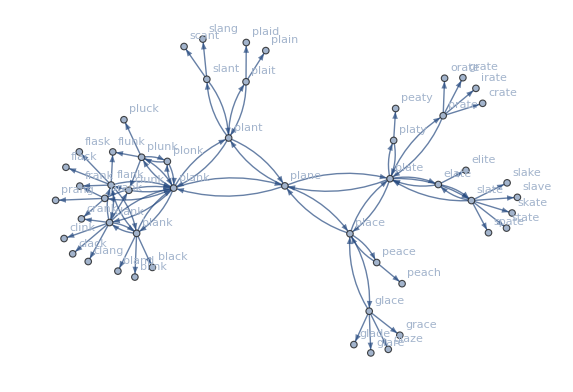

```mathematica
NestGraph[(word↦Select[HammingDistance[word,#]==1&][WordList[]]),"plane",3,VertexLabels->Automatic]
```

```mathematica
WordGraph[dictionary_,start_,nestlevel_]:=NestGraph[(word↦Select[HammingDistance[word,#]==1&][dictionary]),start,nestlevel,VertexLabels->Automatic]
```

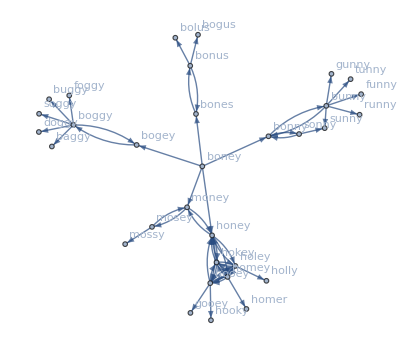

```mathematica
WordGraph[WordList[],"boney",3]
```

Create a github repository:

```mathematica
Needs["Wolfram`GitLink`"]
```

```mathematica
GitOpen@SetDirectory["C:\\Users\\peter\\Documents\\GitHub\\word-cloud-and-graphs-paclet"]
```

<|BareQ→False,GitDirectory→C:\Users\peter\Documents\GitHub\word-cloud-and-graphs-paclet\.git\,WorkingDirectory→C:\Users\peter\Documents\GitHub\word-cloud-and-graphs-paclet\|>

```mathematica
<<CloudObject`
```

```mathematica
<<PacletResource`
```

```mathematica
["Paclet"]
```

```mathematica
GitOpen[SetDirectory["C:\\Users\\peter\\Documents\\GitHub\\association-functions"]]
```

GitOpen[C:\Users\peter\Documents\GitHub\association-functions]

```mathematica
$VersionNumber
```

13.1

```mathematica
Quit
```

XXXX: